## 1. Número de Trigg

### a)

```mathematica
HasDistinctDig[n_Integer]/;IntegerLength[n]<=4:=If[IntegerLength[n]==4,Length[Union[IntegerDigits[n]]]>1, True]
```

```mathematica
FilteredList:=Select[Range[9999],HasDistinctDig]
```

```mathematica
DigList[n_Integer]:=IntegerDigits[n,10,4]
```

```mathematica
N4=Map[DigList,FilteredList]
```

```mathematica
Length[N4]
```

9990

### b)

```mathematica
alfa[n_Integer]:=Sort[IntegerDigits[n,10,4]][[4]]
```

```mathematica
beta[n_Integer]:=Sort[IntegerDigits[n,10,4]][[3]]
```

```mathematica
gamma[n_Integer]:=Sort[IntegerDigits[n,10,4]][[2]]
```

```mathematica
delta[n_Integer]:=Sort[IntegerDigits[n,10,4]][[1]]
```

```mathematica
T[n_Integer]:=FromDigits[{beta[n],alfa[n],delta[n],gamma[n]}]-FromDigits[Reverse[{beta[n],alfa[n],delta[n],gamma[n]}]]
```

```mathematica
T[1023]
```

1269

```mathematica
T[1234]
```

1269

```mathematica
T[5626]
```

1359

### c)

```mathematica
FindFixedPoint[n_Integer]:=NestWhile[T,n,Function[x,T[x]!=x]]
```

```mathematica
IterList[n_Integer]:=NestWhileList[T,n,Function[x,T[x]!=x]]
```

```mathematica
(* Exemplo 1 *)
FindFixedPoint[1023]
```

2538

```mathematica
IterList[1023]
```

{1023,1269,4716,2538}

```mathematica
(*Exemplo 2*)
FindFixedPoint[1234]
```

2538

```mathematica
IterList[1234]
```

{1234,1269,4716,2538}

```mathematica
(*Exemplo 3*)
FindFixedPoint[5626]
```

2538

```mathematica
IterList[5626]
```

{5626,1359,2718,5625,360,3537,2358,2538}

```mathematica
(*Resultados obtidos sob a forma de tabela*)
DataFixedPoint=Transpose[{{1023,1234,5626},Map[IterList,{1023,1234,5626}]}];
Grid[Prepend[DataFixedPoint,{Subscript[n,0],"Lista de Iterações Realizadas"}],Frame->All]
```

n_0 | Lista de Iterações Realizadas
1023 | {1023,1269,4716,2538}
1234 | {1234,1269,4716,2538}
5626 | {5626,1359,2718,5625,360,3537,2358,2538}

### d)

```mathematica
N4List:=Map[FromDigits,N4]
```

```mathematica
Union[Map[FindFixedPoint,N4List]]
```

{2538}

```mathematica
NumIter[n_Integer]:=Length[IterList[n]]-1
NumIterList:=Map[NumIter,N4List]
```

```mathematica
Max[NumIterList]
```

7

```mathematica
NumElementsIter[n_Integer]:= Length[Select[N4List,Function[x,NumIter[x]==n]]]
```

```mathematica
(*Demora cerca de 10s*)
NumElementsIterList=Map[NumElementsIter,Range[Max[NumIterList]]]
```

{383,576,2400,1272,1518,1656,2184}

```mathematica
(*Resultados obtidos sob a forma de tabela*)
DataIter=Transpose[{Range[Max[NumIterList]],NumElementsIterList}];
Grid[Prepend[DataIter,{"i","Número de Elementos "}],Frame->All]
```

i | Número de Elementos 
1 | 383
2 | 576
3 | 2400
4 | 1272
5 | 1518
6 | 1656
7 | 2184

### e)

```mathematica
ListD[n_Integer,p_List]:=Reverse[Sort[IntegerDigits[n,10,Length[p]]]]
```

```mathematica
NumPermut[n_Integer,p_List]:=Map[Function[x,ListD[n,p][[p[[x]]]]],Range[Length[p]]]
```

```mathematica
TP[n_Integer,σ_List,δ_List]:=FromDigits[NumPermut[n,σ]]-FromDigits[NumPermut[n,δ]]
```

### f)

```mathematica
FindFixedPointPermut[n_Integer,σ_List,δ_List]:=NestWhile[Function[x,TP[x,σ,δ]],n,Function[x,TP[x,σ,δ]!=x]]
```

```mathematica
IterListPermut[n_Integer,σ_List,δ_List]:=NestWhileList[Function[x,TP[x,σ,δ]],n,Function[x,TP[x,σ,δ]!=x],1,20]
```

```mathematica
FindFixedPointPermut[1234,{1,2,3,4},{2,1,3,4}] (* Se tentarmos procurar o ponto fixo de 1234 aplicando as permutações (1,2,3,4) e (2,1,3,4) somos levados a suspeitar da existência de um loop infinito! *)
```

$Aborted

```mathematica
IterListPermut[1234,{1,2,3,4},{2,1,3,4}](* Até 20 iterações *)
```

{1234,900,8100,6300,2700,4500,900,8100,6300,2700,4500,900,8100,6300,2700,4500,900,8100,6300,2700,4500}

```mathematica
(* Vericamos que a sequência de números {900,8100,6300,2700,4500} se repete ao longo da procura do ponto fixo, razão que conduz ao loop infinito! *)
```

```mathematica
FindFixedPointPermut[1234,{1,2,3,4},{4,3,2,1}]
```

6174

```mathematica
IterListPermut[1234,{1,2,3,4},{4,3,2,1}]
```

{1234,3087,8352,6174}

```mathematica
FindFixedPointPermut[1234,{2,4,3,1},{3,2,4,1}]
```

0

```mathematica
ListIterPermut[1234,{2,4,3,1},{3,2,4,1}]
```

ListIterPermut[1234,{2,4,3,1},{3,2,4,1}]

## 2. Números Coprimos

### b)

```mathematica
aleatorios[m_,n_]:=RandomInteger[{1,m},{n,2}]
```

### c)

```mathematica
Probabilidade[m_,n_]:=Module[{coprimes=0,list,i},list=aleatorios[m,n];
Do[If[GCD[list[[i,1]],list[[i,2]]]==1,coprimes++],{i,Length[list]}];
coprimes/n]
```

### d)

```mathematica
MNList:=Map[Function[x,10^x],Range[6]]
```

```mathematica
DataProb:=Table[N[Probabilidade[m,n]],{n,MNList},{m,MNList}]
```

```mathematica
DataProbInfo:=MapThread[Prepend,{DataProb,MNList}]
```

```mathematica
HeaderRow:=Prepend[MNList,"n\\m"]
```

```mathematica
TableProb=Grid[Prepend[DataProbInfo,HeaderRow],Frame->All]
```

n\m | 10 | 100 | 1000 | 10000 | 100000 | 1000000
10 | 0.4 | 0.8 | 0.7 | 0.8 | 0.6 | 0.8
100 | 0.72 | 0.63 | 0.58 | 0.59 | 0.59 | 0.63
1000 | 0.602 | 0.628 | 0.592 | 0.571 | 0.62 | 0.62
10000 | 0.6281 | 0.6156 | 0.6075 | 0.6097 | 0.5997 | 0.6083
100000 | 0.62814 | 0.60978 | 0.60793 | 0.6112 | 0.60956 | 0.60511
1000000 | 0.631167 | 0.608948 | 0.608425 | 0.608031 | 0.607317 | 0.608078

```mathematica
AbsError[m_Integer,n_Integer]:= Abs[(6/Pi^2)-N[Probabilidade[m,n]]]
```

```mathematica
DataAbsError:=Table[AbsError[m,n],{n,MNList},{m,MNList}]
```

```mathematica
DataAbsErrorInfo:=MapThread[Prepend,{DataAbsError,MNList}]
```

```mathematica
TableAbsError=Grid[Prepend[DataAbsErrorInfo,HeaderRow],Frame->All]
```

n\m | 10 | 100 | 1000 | 10000 | 100000 | 1000000
10 | 0.107927 | 0.0079271 | 0.0079271 | 0.0920729 | 0.307927 | 0.0920729
100 | 0.0420729 | 0.0379271 | 0.0120729 | 0.0179271 | 0.0079271 | 0.117927
1000 | 0.0099271 | 0.0190729 | 0.0369271 | 0.0090729 | 0.0229271 | 0.0090729
10000 | 0.0163729 | 0.0027271 | 0.0014271 | 0.0012271 | 0.0078729 | 0.000472898
100000 | 0.0250029 | 0.0019529 | 0.000162898 | 0.0018871 | 0.0012729 | 0.0013829
1000000 | 0.0212639 | 0.0013739 | 0.000499898 | 0.000159898 | 0.000620102 | 0.000418898

## 3. Formiga de Langton

### a)

```mathematica
LangtonsAnt[n_Integer,d_String,kmax_Integer]:=Module[
{
size=2 n+1,
grid,
pos={n+1,n+1},
dir,
step=0,
rotateClockwise,
rotateAntiClockwise
},

rotateClockwise[{dr_,dc_}]:={dc,-dr};
rotateAntiClockwise[{dr_,dc_}]:={-dc,dr};
grid=ConstantArray[0,{size,size}];
dir=Switch[d,"Cima",{-1,0},"Baixo",{1,0},"Esquerda",{0,-1},"Direita",{0,1}];

While[step<kmax&&1<=pos[[1]]<=size&&1<=pos[[2]]<=size,
If[grid[[pos[[1]],pos[[2]]]]==1,
dir=rotateClockwise[dir],
dir=rotateAntiClockwise[dir] (* If grid[[pos[[1]],pos[[2]]]]==0 *)
];

grid[[pos[[1]],pos[[2]]]]=1-grid[[pos[[1]],pos[[2]]]];
pos=pos+dir;
step++;
];

grid
];
```

### b)

```mathematica
kmax={250,500,750,1000};
matrices=LangtonsAnt[12,"Direita",#]&/@kmax;
labels=("k_max = "<>ToString[#])&/@kmax;
MapThread[ArrayPlot[#1,PlotLabel->#2]&,{matrices,labels}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
kmax={9000,9500,10000,10500,11000};
matrices=LangtonsAnt[38,"Direita",#]&/@kmax;
labels=("k_max = "<>ToString[#])&/@kmax;
MapThread[ArrayPlot[#1,PlotLabel->#2]&,{matrices,labels}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### c)

```mathematica
(* O padrão encontra-se a partir dos valores finais da direção, pelo que se acrescenta ao output *)
LangtonsAnt[n_Integer,d_String,kmax_Integer]:=Module[
{
size=2 n+1,
grid,
pos={n+1,n+1},
dir,
step=0,
rotateClockwise,
rotateAntiClockwise
},

rotateClockwise[{dr_,dc_}]:={dc,-dr};
rotateAntiClockwise[{dr_,dc_}]:={-dc,dr};
grid=ConstantArray[0,{size,size}];
dir=Switch[d,"Cima",{-1,0},"Baixo",{1,0},"Esquerda",{0,-1},"Direita",{0,1}];

While[step<kmax&&1<=pos[[1]]<=size&&1<=pos[[2]]<=size,
If[grid[[pos[[1]],pos[[2]]]]==1,
dir=rotateAntiClockWise[dir],
dir=rotateAntiClockwise[dir] (* If grid[[pos[[1]],pos[[2]]]]==0 *)
];

grid[[pos[[1]],pos[[2]]]]=1-grid[[pos[[1]],pos[[2]]]];
pos=pos+dir;
step++;
];

{grid,dir}
];
```

```mathematica
(* Argumentos da função *)
initial=10000;
final=11000;
n=38;
d="Direita";

(* Primeiro e último valores de kmax no intervalo a usar *)
matrices=LangtonsAnt[n,d,#][[1]]&/@{initial,final};
labels={"Initial","Final"};
plot=MapThread[ArrayPlot[#1,PlotLabel->#2]&,{matrices,labels}];
Print[plot];

(* Evolução da direção final ao longo do intervalo *)
dirs=LangtonsAnt[n,d,#][[2]]&/@Range[initial,final];
period=FindRepeat[dirs];
Print[period];
Length[period]
```

{-Graphics-,-Graphics-}

{{0,1},{1,0},{0,-1},{1,0},{0,-1},{1,0},{0,1},{-1,0},{0,-1},{-1,0},{0,-1},{-1,0},{0,1},{1,0},{0,-1},{1,0},{0,1},{-1,0},{0,-1},{-1,0},{0,-1},{1,0},{0,-1},{1,0},{0,1},{-1,0},{0,-1},{-1,0},{0,1},{1,0},{0,-1},{1,0},{0,-1},{1,0},{0,1},{-1,0},{0,-1},{-1,0},{0,-1},{1,0},{0,1},{-1,0},{0,1},{1,0},{0,-1},{-1,0},{0,-1},{-1,0},{0,-1},{1,0},{0,1},{-1,0},{0,1},{-1,0},{0,1},{1,0},{0,1},{-1,0},{0,1},{1,0},{0,-1},{-1,0},{0,-1},{1,0},{0,-1},{-1,0},{0,-1},{1,0},{0,1},{-1,0},{0,1},{1,0},{0,1},{-1,0},{0,1},{-1,0},{0,1},{1,0},{0,1},{1,0},{0,-1},{1,0},{0,-1},{1,0},{0,-1},{-1,0},{0,-1},{1,0},{0,1},{-1,0},{0,1},{1,0},{0,1},{1,0},{0,-1},{1,0},{0,1},{-1,0},{0,-1},{-1,0},{0,1},{-1,0},{0,-1},{1,0}}

104

### d)

```mathematica
LangtonsAnt[n_Integer,d_String,kmax_Integer, r_String]:=Module[
{
size=2 n+1,
grid,
pos={n+1,n+1},
dir,
step=0,
rotateAntiClockWise,
rotateAntiClockwise,
rules=Characters[r],
nRules=StringLength[r],
color
},

rotateAntiClockWise[{dr_,dc_}]:={dc,-dr};
rotateAntiClockWise[{dr_,dc_}]:={-dc,dr};
grid=ConstantArray[0,{size,size}];
dir=Switch[d,"Cima",{-1,0},"Baixo",{1,0},"Esquerda",{0,-1},"Direita",{0,1}];

While[step<kmax&&1<=pos[[1]]<=size&&1<=pos[[2]]<=size,
color=grid[[pos[[1]],pos[[2]]]];

If[rules[[color+1]]=="N",
dir=rotateAntiClockWise[dir],
dir=rotateAntiClockWise[dir] (* If grid[[pos[[1]],pos[[2]]]]=="P" *)
];

grid[[pos[[1]],pos[[2]]]]=Mod[color+1,nRules];
pos=pos+dir;
step++;
];

grid
];
```

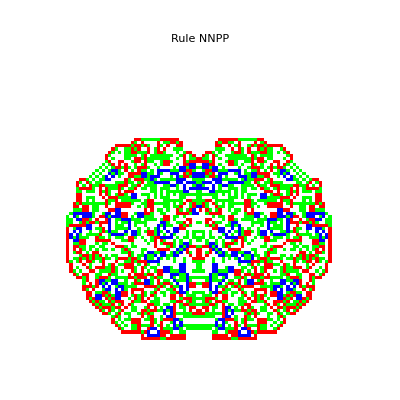
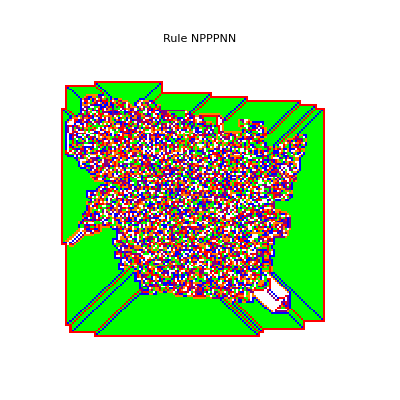
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
n={50,80,700};
rules={"NNPP","NPPPNN","PPNNNPNPNPPN"};
colors={0->White,1->Red,2->Green,3->Blue,4->Orange,5->Purple,6->Black,7->Yellow,8->Cyan,9->Pink,10->Gray,11->Brown};
matrices=MapThread[LangtonsAnt[#1,"Direita",500000,#2]&,{n,rules}];
labels=("Rule "<>ToString[#])&/@rules;
MapThread[ArrayPlot[#1,ColorRules->colors,PlotLabel->#2]&,{matrices,labels}]
```